# Homework 34-35

## Problem 34.1

A ring of diameter R = 30 cm has six identical masses with m= 125 g arranged around it. The masses move without friction on the ring. Each pair of masses is connected by a spring of spring constant k = 2.50 N/m, as shown below. When each angle is zero, the springs are in equilibrium. Ignore any effect of the curvature on the behavior of the spring (in other words, you can use the arc length along the circumference of the ring as your distance x in U = 1/2 k x^2.)
-Graphics-
Find and describe the normal frequencies and the normal modes of oscillation for the system. Use the angular displacement from the equilibrium angle for each mass as the coordinates. Call these theta1, theta2, etc. The ring is horizontal so we can ignore the force of gravity.

```mathematica
Quit[]
```

To solve this problem, we will need to construct the appropriate matrices that represent the equations of motion. There are two approaches that I would suggest. You can do either one.

Approach 1: Construct the Lagrangian and find the equations of motion in the usual way. Since this is a bit complicated for all the masses, let us begin by considering just a single mass; let’s say mass #3. Find all the terms in the Lagrangian that contain theta3 or theta3dot. Then find the equations of motion for mass3. Based on this result, you can determine the corresponding equations of motion for all the other masses just shifting all of your subscripts based on which mass you are considering. You can then put together your matrix equation. If you choose this approach, complete the cells where you write down the Lagrangian and equations of motion for particle 3.

Approach 2: Read off the components of the M and K matrices directly by looking at the form of T and U, as described in sections 11.5-11.6 and Lecture 35.

### Preliminaries for approach 1 (complete this if you are choosing this approach; otherwise, skip to the next part)

Write down the terms of the Lagrangian containing theta3 and theta3dot. Call it L3. Then determine the conjugate momentum (p3) and the derivative with respect to theta3 and use these to generate the equations of motion for theta3.

```mathematica
L3="????"
rule={theta3->theta3[t],theta3dot->theta3'[t],theta2->theta2[t],theta4->theta4[t]};
p3="????"/.rule
dLdtheta3="????"/.rule
eq3="????"=="????"
```

From the equations of motion for mass 3, you should be able to generate the equations for all the others just by shifting the subscripts. Once you have completed this part, skip down to the part where you construct the matrices.

### Solutions

```mathematica
L$=m/2*R^2*theta3dot^2-k/2*R^2*(theta4-theta3)^2-k/2*R^2*(theta3-theta2)^2;
p3$=D[L$,theta3dot]/.rule;
dLdtheta3$=D[L$,theta3]/.rule;
If[FullSimplify[Solve[L3==L$,R]]=={{}},Print["L3 is correct."],Print["L3 is incorrect."]]
If[FullSimplify[Solve[p3==p3$,R]]=={{}},Print["p3 is correct."],Print["p3 is incorrect."]]
If[FullSimplify[Solve[dLdtheta3==dLdtheta3$,R]]=={{}},Print["dLdtheta3 is correct."],Print["dLdtheta3 is incorrect."]]

eq3A$=eq3/.{theta3''[t]->Dth2,theta3'[t]->Dth};
eq3$=D[m*R^2*theta3'[t],t]==k*R^2*(theta4[t]-theta3[t])-k*R^2*(theta3[t]-theta2[t]);
eq3B$=eq3$/.{theta3''[t]->Dth2,theta3'[t]->Dth};
aA$=k/.Solve[eq3A$,k][[1]];
aB$=k/.Solve[eq3B$,k][[1]];
If[FullSimplify[Solve[aA$==aB$,m]]=={{}},Print["eq3 is correct."],Print["eq3 is incorrect."]]
```

### Preliminaries for approach 2 (skip if you chose approach 1)

To make things manageable, write down T and U for just one of the masses; let’s say mass 3. Expand any squared quantities you have in your expression for U.

```mathematica
T3 = m*R^2*theta3dot^2/2
U3 =k*R^2*((theta3 - theta4)^2 + (theta3 - theta2)^2)/2
```

1/2 m R^2 theta3dot^2

1/2 k R^2 ((-theta2+theta3)^2+(theta3-theta4)^2)

Referring to equations 11.51 and 11.53, we see that the terms in T have the form 1/2*Mjk*thetajdot*thetakdot, where Ajk is the element in row j, column k of the M matrix. Likewise, terms in U have the form 1/2 Kjk*thetaj*thetak, where Kjk is the element in row j, column k of the K matrix. Look at all the terms in T and U with a subscript 3 (i.e. theta3 or theta3dot) and read off the coefficients to identify the corresponding elements in the M and K matrices. HINT: The coefficients on terms in U containing the product of two different coordinates should be divided by 2 when placing them in the K matrix, since those terms show up twice in the matrix (i.e. in position j,k as well as position k,j).

```mathematica
M33=m*R^2
K33=2*k*R^2
K32 = -k*R^2
K34 = -k*R^2
```

m R^2

2 k R^2

-k R^2

-k R^2

From these matrix elements, you should be able to generate the remaining elements in the M and K matrices just by shifting the subscripts. Once you have completed this part, skip down to the part where you construct the matrices.

### Solutions

```mathematica
T3$ = 1/2 m R^2 theta3dot^2;
U3$ = 1/2 k R^2(theta2^2 + 2theta3^2 +theta4^2 - 2 theta3 theta2 - 2 theta4 theta3);
If[FullSimplify[Solve[T3==T3$,R]]=={{}},Print["T3 is correct."],Print["T3 is incorrect."]]
If[FullSimplify[Solve[U3==U3$,R]]=={{}},Print["U3 is correct."],Print["U3 is incorrect."]]

M33$=m R^2;
K33$=2 k R^2;
K32$ = -k R^2;
K34$ = - k R^2;
If[FullSimplify[Solve[M33==M33$,R]]=={{}},Print["M33 is correct."],Print["M33 is incorrect."]]
If[FullSimplify[Solve[K33==K33$,R]]=={{}},Print["K33 is correct."],Print["K33 is incorrect."]]
If[FullSimplify[Solve[K32==K32$,R]]=={{}},Print["K32 is correct."],Print["K32 is incorrect."]]
If[FullSimplify[Solve[K34==K34$,R]]=={{}},Print["K34 is correct."],Print["K34 is incorrect."]]
```

T3 is correct.

U3 is correct.

M33 is correct.

K33 is correct.

K32 is correct.

K34 is correct.

### Construct the M and K matrices and use them to calculate the normal mode frequencies and displacement patterns.

Let R be the radius of the ring, k be the spring constant, and m be the mass of each particle.

```mathematica
Mmat={{M33, 0, 0, 0, 0, 0}, {0, M33, 0, 0, 0, 0}, {0, 0, M33, 0, 0, 0} ,{0, 0, 0, M33, 0, 0}, {0, 0, 0, 0, M33, 0}, {0, 0, 0, 0, 0, M33}   };Mmat//MatrixForm
Kmat={{k*R^2*2, k*R^2*-1, 0, 0, 0, k*R^2*-1}  ,{k*R^2*-1, k*R^2*2, k*R^2*-1, 0, 0, 0}, {0, k*R^2*-1, k*R^2*2, k*R^2*-1, 0, 0}, {0, 0,k*R^2*-1,k*R^2* 2,k*R^2* -1, 0} , {0, 0, 0, k*R^2*-1,k*R^2* 2,k*R^2* -1}, {k*R^2*-1, 0, 0, 0, k*R^2*-1,k*R^2* 2} };Kmat//MatrixForm
MinvK=Inverse[Mmat].Kmat;
sol=Simplify[Eigensystem[MinvK]]
```

(m R^2 | 0 | 0 | 0 | 0 | 0
0 | m R^2 | 0 | 0 | 0 | 0
0 | 0 | m R^2 | 0 | 0 | 0
0 | 0 | 0 | m R^2 | 0 | 0
0 | 0 | 0 | 0 | m R^2 | 0
0 | 0 | 0 | 0 | 0 | m R^2)

(2 k R^2 | -k R^2 | 0 | 0 | 0 | -k R^2
-k R^2 | 2 k R^2 | -k R^2 | 0 | 0 | 0
0 | -k R^2 | 2 k R^2 | -k R^2 | 0 | 0
0 | 0 | -k R^2 | 2 k R^2 | -k R^2 | 0
0 | 0 | 0 | -k R^2 | 2 k R^2 | -k R^2
-k R^2 | 0 | 0 | 0 | -k R^2 | 2 k R^2)

{{(4 k)/m,(3 k)/m,(3 k)/m,k/m,k/m,0},{{-1,1,-1,1,-1,1},{-1,0,1,-1,0,1},{-1,1,0,-1,1,0},{1,0,-1,-1,0,1},{-1,-1,0,1,1,0},{1,1,1,1,1,1}}}

### Solution

```mathematica
M$=m R^2 {{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
If[FullSimplify[Mmat]==FullSimplify[M$],Print["Mmat is correct."],Print["The following elements of Mmat are incorrect:"]];
For[i=1,i<7,i++,
For[j=0,j<6,j++
(*Print[i," ",j];*)
If[FullSimplify[Mmat[[i,j]]]==FullSimplify[M$[[i,j]]],,Print["Mmat[",i,",",j,"]",Mmat[[i,j]]," should be ",M$[[i,j]]]]
]]

K$=k R^2 {{2,-1,0,0,0,-1},{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1},{-1,0,0,0,-1,2}};
If[FullSimplify[Kmat]==FullSimplify[K$],Print["Kmat is correct."],Print["The following elements of Kmat are incorrect:"]];
For[i=1,i<7,i++,
For[j=0,j<6,j++
(*Print[i," ",j];*)
If[FullSimplify[Kmat[[i,j]]]==FullSimplify[K$[[i,j]]],,Print["Kmat[",i,",",j,"]",Kmat[[i,j]]," should be ",K$[[i,j]]]]
]]
```

Mmat is correct.

Kmat is correct.

The eigenvalues (i.e. squared frequencies) and eigenvectors should be:
{{(4 k)/m,(3 k)/m,(3 k)/m,k/m,k/m,0},{{-1,1,-1,1,-1,1},{-1,0,1,-1,0,1},{-1,1,0,-1,1,0},{1,0,-1,-1,0,1},{-1,-1,0,1,1,0},{1,1,1,1,1,1}}}
Note that the order may be somewhat different for you.

### Look at the eigenvectors corresponding to each eigenvalue and use these to describe qualitatively the motion associated with each mode.

Highest frequency mode: (Type a brief qualitative description of the motion)
The highest frequency node belongs to the largest oscillator and has value 2 √(k/m). Notice the eigenvector in this case is (-1, 1, -1, 1, -1, 1) which means that neighboring masses oscillate opposite each other. In other words the whole ring is vibrating where mass 1 vibrates opposite to mass 6 and mass 2 and mass 2 vibrates opposite to mass 1 and mass 3, etc.

### Solution

--Alternate masses move in opposite directions with equal amplitude.
or
--Pairs of masses oscillate out of phase with respect to each other, but with the same amplitude.

The two degenerate modes with the second highest frequency:  (Type a brief qualitative description of the motion)
In this case the eigenvectors are (-1, 0, 1, -1, 0, 1) and (-1, 1, 0, -1, 1, 0) in both cases two particles opposite each other remain stationary. In the first case is is mass 2 and 5 and in the second case it is mass 3 and 6. Then the two masses in-between the stationary ones oscillate opposite one another.

### Solution

Two particles opposite each other on the ring remain stationary. Going around the ring in either direction, the two masses between the stationary masses are moving out of phase with each other.

The two degenerate modes with the third highest frequency:  (Type a brief qualitative description of the motion)
In this case the eigenvectors are (1, 0, -1, -1, 0, 1) and (-1, -1, 0, 1, 1, 0). The same masses as in the previous problem remain stationary (i.e. mass 2 and 5 and mass 3 and 6 respectively). Then the masses in-between the stationary ones oscillate in unison.

### Solution

Two particles opposite each other on the ring remain stationary. Going around the ring in either direction, the two masses between the stationary masses are moving in of phase with each other, although these two pairs of in-phase masses are out of phase with each other.

The mode with the lowest frequency:  (Type a brief qualitative description of the motion)
In this case our eigenvector is a vector of all 1s with angular frequency 0. This means that the masses are either stationary or rotate uniformly around the ring together. In other words there is no relative motion between the masses.

### Solution

All the masses move uniformly around the circle together.

### Full solutions

Click through the cells below to enjoy animations of the various normal modes. Look at the initial conditions on the theta values for each mode and make sure you understand why the particular initial conditions required to excite each mode are the way they are (Hint: they have to match the eigenvectors for each mode).

```mathematica
Clear["`*"]
```

```mathematica
Mmat=m R^2 {{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};

Kmat=k R^2 {{2,-1,0,0,0,-1},{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1},{-1,0,0,0,-1,2}};


thetavec={theta1[t],theta2[t],theta3[t],theta4[t],theta5[t],theta6[t]};

thetavecdotdot={theta1''[t],theta2''[t],theta3''[t],theta4''[t],theta5''[t],theta6''[t]};

system=Mmat.thetavecdotdot==-Kmat.thetavec
```

{m R^2 theta1''[t],m R^2 theta2''[t],m R^2 theta3''[t],m R^2 theta4''[t],m R^2 theta5''[t],m R^2 theta6''[t]}=={-2 k R^2 theta1[t]+k R^2 theta2[t]+k R^2 theta6[t],k R^2 theta1[t]-2 k R^2 theta2[t]+k R^2 theta3[t],k R^2 theta2[t]-2 k R^2 theta3[t]+k R^2 theta4[t],k R^2 theta3[t]-2 k R^2 theta4[t]+k R^2 theta5[t],k R^2 theta4[t]-2 k R^2 theta5[t]+k R^2 theta6[t],k R^2 theta1[t]+k R^2 theta5[t]-2 k R^2 theta6[t]}

### Highest frequency

```mathematica
bc0={theta1'[0]==0,theta2'[0]==0,theta3'[0]==0,theta4'[0]==0,theta5'[0]==0,theta6'[0]==0};
bc1={theta1[0]==a,theta2[0]==-a,theta3[0]==a,theta4[0]==-a,theta5[0]==a,theta6[0]==-a};
sol4:=DSolve[{system,bc0[[1]],bc0[[2]],bc0[[3]],bc0[[4]],bc0[[5]],bc0[[6]],bc1[[1]],bc1[[2]],bc1[[3]],bc1[[4]],bc1[[5]],bc1[[6]]},{theta1,theta2,theta3,theta4,theta5,theta6},t];
```

The code below is a little trick to put the solutions in a more recognizable form. (You have to be just a bit patient as your wait for it to do its magic.)

```mathematica
Theta1=FullSimplify[ExpToTrig[theta1[t]/.sol4]]
Theta2=FullSimplify[ExpToTrig[theta2[t]/.sol4]]
Theta3=FullSimplify[ExpToTrig[theta3[t]/.sol4]]
Theta4=FullSimplify[ExpToTrig[theta4[t]/.sol4]]
Theta5=FullSimplify[ExpToTrig[theta5[t]/.sol4]]
Theta6=FullSimplify[ExpToTrig[theta6[t]/.sol4]]
```

{a Cos[(2 √k t)/(√m)]}

{-a Cos[(2 √k t)/(√m)]}

{a Cos[(2 √k t)/(√m)]}

{-a Cos[(2 √k t)/(√m)]}

{a Cos[(2 √k t)/(√m)]}

{-a Cos[(2 √k t)/(√m)]}

You should note that each mass moves with the same frequency -- that's the definition of a normal mode. Also, the frequency magically turns out to be the frequency predicted for the highest energy mode!

```mathematica
rep={R->0.3,k->2.5,m->0.125,a->0.1};
diskr=0.05;
R1[t_]={((R Cos[0Pi/3+Theta1])/.rep)[[1]],((R Sin[0Pi/3+Theta1])/.rep)[[1]]};
R2[t_]={((R Cos[1Pi/3+Theta2])/.rep)[[1]],((R Sin[1Pi/3+Theta2])/.rep)[[1]]};
R3[t_]={((R Cos[2Pi/3+Theta3])/.rep)[[1]],((R Sin[2Pi/3+Theta3])/.rep)[[1]]};
R4[t_]={((R Cos[3Pi/3+Theta4])/.rep)[[1]],((R Sin[3Pi/3+Theta4])/.rep)[[1]]};
R5[t_]={((R Cos[4Pi/3+Theta5])/.rep)[[1]],((R Sin[4Pi/3+Theta5])/.rep)[[1]]};
R6[t_]={((R Cos[5Pi/3+Theta6])/.rep)[[1]],((R Sin[5Pi/3+Theta6])/.rep)[[1]]};
Manipulate[Graphics[{Black,Line[{{-0.4,-0.4},{-0.4,0.4},{0.4,0.4},{0.4,-0.4},{-0.4,-0.4}}], Circle[{0,0},R]/.rep,Gray,Disk[R1[t],diskr],Disk[R2[t],diskr],Disk[R3[t],diskr],Disk[R4[t],diskr],Disk[R5[t],diskr],Disk[R6[t],diskr]}],{t,0.0,2}]
```

### Second highest frequency

```mathematica
bc0={theta1'[0]==0,theta2'[0]==0,theta3'[0]==0,theta4'[0]==0,theta5'[0]==0,theta6'[0]==0};
bc1={theta1[0]==-a,theta2[0]==0,theta3[0]==a,theta4[0]==-a,theta5[0]==0,theta6[0]==a};
sol3:=DSolve[{system,bc0[[1]],bc0[[2]],bc0[[3]],bc0[[4]],bc0[[5]],bc0[[6]],bc1[[1]],bc1[[2]],bc1[[3]],bc1[[4]],bc1[[5]],bc1[[6]]},{theta1,theta2,theta3,theta4,theta5,theta6},t];

Theta1=FullSimplify[ExpToTrig[theta1[t]/.sol3]]
Theta2=FullSimplify[ExpToTrig[theta2[t]/.sol3]]
Theta3=FullSimplify[ExpToTrig[theta3[t]/.sol3]]
Theta4=FullSimplify[ExpToTrig[theta4[t]/.sol3]]
Theta5=FullSimplify[ExpToTrig[theta5[t]/.sol3]]
Theta6=FullSimplify[ExpToTrig[theta6[t]/.sol3]]

rep={R->0.3,k->2.5,m->0.125,a->0.1};
diskr=0.05;
R1[t_]={((R Cos[0Pi/3+Theta1])/.rep)[[1]],((R Sin[0Pi/3+Theta1])/.rep)[[1]]};
R2[t_]={((R Cos[1Pi/3+Theta2])/.rep)[[1]],((R Sin[1Pi/3+Theta2])/.rep)[[1]]};
R3[t_]={((R Cos[2Pi/3+Theta3])/.rep)[[1]],((R Sin[2Pi/3+Theta3])/.rep)[[1]]};
R4[t_]={((R Cos[3Pi/3+Theta4])/.rep)[[1]],((R Sin[3Pi/3+Theta4])/.rep)[[1]]};
R5[t_]={((R Cos[4Pi/3+Theta5])/.rep)[[1]],((R Sin[4Pi/3+Theta5])/.rep)[[1]]};
R6[t_]={((R Cos[5Pi/3+Theta6])/.rep)[[1]],((R Sin[5Pi/3+Theta6])/.rep)[[1]]};
Manipulate[Graphics[{Black,Line[{{-0.4,-0.4},{-0.4,0.4},{0.4,0.4},{0.4,-0.4},{-0.4,-0.4}}], Circle[{0,0},R]/.rep,Gray,Disk[R1[t],diskr],Disk[R2[t],diskr],Disk[R3[t],diskr],Disk[R4[t],diskr],Disk[R5[t],diskr],Disk[R6[t],diskr]}],{t,0.0,3}]
```

{-a Cos[(√3 √k t)/(√m)]}

{0}

{a Cos[(√3 √k t)/(√m)]}

{-a Cos[(√3 √k t)/(√m)]}

{0}

{a Cos[(√3 √k t)/(√m)]}

### Third highest frequency

```mathematica
bc0={theta1'[0]==0,theta2'[0]==0,theta3'[0]==0,theta4'[0]==0,theta5'[0]==0,theta6'[0]==0};
bc1={theta1[0]==a,theta2[0]==0,theta3[0]==-a,theta4[0]==-a,theta5[0]==0,theta6[0]==a};
sol2:=DSolve[{system,bc0[[1]],bc0[[2]],bc0[[3]],bc0[[4]],bc0[[5]],bc0[[6]],bc1[[1]],bc1[[2]],bc1[[3]],bc1[[4]],bc1[[5]],bc1[[6]]},{theta1,theta2,theta3,theta4,theta5,theta6},t];

Theta1=FullSimplify[ExpToTrig[theta1[t]/.sol2]]
Theta2=FullSimplify[ExpToTrig[theta2[t]/.sol2]]
Theta3=FullSimplify[ExpToTrig[theta3[t]/.sol2]]
Theta4=FullSimplify[ExpToTrig[theta4[t]/.sol2]]
Theta5=FullSimplify[ExpToTrig[theta5[t]/.sol2]]
Theta6=FullSimplify[ExpToTrig[theta6[t]/.sol2]]

rep={R->0.3,k->2.5,m->0.125,a->0.1};
diskr=0.05;
R1[t_]={((R Cos[0Pi/3+Theta1])/.rep)[[1]],((R Sin[0Pi/3+Theta1])/.rep)[[1]]};
R2[t_]={((R Cos[1Pi/3+Theta2])/.rep)[[1]],((R Sin[1Pi/3+Theta2])/.rep)[[1]]};
R3[t_]={((R Cos[2Pi/3+Theta3])/.rep)[[1]],((R Sin[2Pi/3+Theta3])/.rep)[[1]]};
R4[t_]={((R Cos[3Pi/3+Theta4])/.rep)[[1]],((R Sin[3Pi/3+Theta4])/.rep)[[1]]};
R5[t_]={((R Cos[4Pi/3+Theta5])/.rep)[[1]],((R Sin[4Pi/3+Theta5])/.rep)[[1]]};
R6[t_]={((R Cos[5Pi/3+Theta6])/.rep)[[1]],((R Sin[5Pi/3+Theta6])/.rep)[[1]]};
Manipulate[Graphics[{Black,Line[{{-0.4,-0.4},{-0.4,0.4},{0.4,0.4},{0.4,-0.4},{-0.4,-0.4}}], Circle[{0,0},R]/.rep,Gray,Disk[R1[t],diskr],Disk[R2[t],diskr],Disk[R3[t],diskr],Disk[R4[t],diskr],Disk[R5[t],diskr],Disk[R6[t],diskr]}],{t,0.0,4}]
```

{a Cos[(√k t)/(√m)]}

{0}

{-a Cos[(√k t)/(√m)]}

{-a Cos[(√k t)/(√m)]}

{0}

{a Cos[(√k t)/(√m)]}

### Lowest frequency

```mathematica
w0=Pi/10;
bc0={theta1'[0]==w0,theta2'[0]==w0,theta3'[0]==w0,theta4'[0]==w0,theta5'[0]==w0,theta6'[0]==w0};
bc1={theta1[0]==0,theta2[0]==0,theta3[0]==0,theta4[0]==0,theta5[0]==0,theta6[0]==0};
sol1:=DSolve[{system,bc0[[1]],bc0[[2]],bc0[[3]],bc0[[4]],bc0[[5]],bc0[[6]],bc1[[1]],bc1[[2]],bc1[[3]],bc1[[4]],bc1[[5]],bc1[[6]]},{theta1,theta2,theta3,theta4,theta5,theta6},t];

Theta1=FullSimplify[ExpToTrig[theta1[t]/.sol1]]
Theta2=FullSimplify[ExpToTrig[theta2[t]/.sol1]]
Theta3=FullSimplify[ExpToTrig[theta3[t]/.sol1]]
Theta4=FullSimplify[ExpToTrig[theta4[t]/.sol1]]
Theta5=FullSimplify[ExpToTrig[theta5[t]/.sol1]]
Theta6=FullSimplify[ExpToTrig[theta6[t]/.sol1]]

rep={R->0.3,k->2.5,m->0.125,a->0.1};
diskr=0.05;
R1[t_]={((R Cos[0Pi/3+Theta1])/.rep)[[1]],((R Sin[0Pi/3+Theta1])/.rep)[[1]]};
R2[t_]={((R Cos[1Pi/3+Theta2])/.rep)[[1]],((R Sin[1Pi/3+Theta2])/.rep)[[1]]};
R3[t_]={((R Cos[2Pi/3+Theta3])/.rep)[[1]],((R Sin[2Pi/3+Theta3])/.rep)[[1]]};
R4[t_]={((R Cos[3Pi/3+Theta4])/.rep)[[1]],((R Sin[3Pi/3+Theta4])/.rep)[[1]]};
R5[t_]={((R Cos[4Pi/3+Theta5])/.rep)[[1]],((R Sin[4Pi/3+Theta5])/.rep)[[1]]};
R6[t_]={((R Cos[5Pi/3+Theta6])/.rep)[[1]],((R Sin[5Pi/3+Theta6])/.rep)[[1]]};
Manipulate[Graphics[{Black,Line[{{-0.4,-0.4},{-0.4,0.4},{0.4,0.4},{0.4,-0.4},{-0.4,-0.4}}], Circle[{0,0},R]/.rep,Gray,Disk[R1[t],diskr],Disk[R2[t],diskr],Disk[R3[t],diskr],Disk[R4[t],diskr],Disk[R5[t],diskr],Disk[R6[t],diskr]}],{t,0.0,10}]
```

{(π t)/10}

{(π t)/10}

{(π t)/10}

«3 more identical outputs»

### Arbitrary motion

```mathematica
bc0={theta1'[0]==0,theta2'[0]==0,theta3'[0]==0,theta4'[0]==0,theta5'[0]==0,theta6'[0]==0};
bc1={theta1[0]==a,theta2[0]==0,theta3[0]==0,theta4[0]==0,theta5[0]==0,theta6[0]==0};
solarb:=DSolve[{system,bc0[[1]],bc0[[2]],bc0[[3]],bc0[[4]],bc0[[5]],bc0[[6]],bc1[[1]],bc1[[2]],bc1[[3]],bc1[[4]],bc1[[5]],bc1[[6]]},{theta1,theta2,theta3,theta4,theta5,theta6},t];

Theta1=FullSimplify[ExpToTrig[theta1[t]/.solarb]]
Theta2=FullSimplify[ExpToTrig[theta2[t]/.solarb]]
Theta3=FullSimplify[ExpToTrig[theta3[t]/.solarb]]
Theta4=FullSimplify[ExpToTrig[theta4[t]/.solarb]]
Theta5=FullSimplify[ExpToTrig[theta5[t]/.solarb]]
Theta6=FullSimplify[ExpToTrig[theta6[t]/.solarb]]

rep={R->0.3,k->2.5,m->0.125,a->0.2};
diskr=0.05;
R1[t_]={((R Cos[0Pi/3+Theta1])/.rep)[[1]],((R Sin[0Pi/3+Theta1])/.rep)[[1]]};
R2[t_]={((R Cos[1Pi/3+Theta2])/.rep)[[1]],((R Sin[1Pi/3+Theta2])/.rep)[[1]]};
R3[t_]={((R Cos[2Pi/3+Theta3])/.rep)[[1]],((R Sin[2Pi/3+Theta3])/.rep)[[1]]};
R4[t_]={((R Cos[3Pi/3+Theta4])/.rep)[[1]],((R Sin[3Pi/3+Theta4])/.rep)[[1]]};
R5[t_]={((R Cos[4Pi/3+Theta5])/.rep)[[1]],((R Sin[4Pi/3+Theta5])/.rep)[[1]]};
R6[t_]={((R Cos[5Pi/3+Theta6])/.rep)[[1]],((R Sin[5Pi/3+Theta6])/.rep)[[1]]};
Manipulate[Graphics[{Black,Line[{{-0.4,-0.4},{-0.4,0.4},{0.4,0.4},{0.4,-0.4},{-0.4,-0.4}}], Circle[{0,0},R]/.rep,Gray,Disk[R1[t],diskr],Disk[R2[t],diskr],Disk[R3[t],diskr],Disk[R4[t],diskr],Disk[R5[t],diskr],Disk[R6[t],diskr]}],{t,0.0,4}]
```

{1/6 a (1+2 Cos[(√k t)/(√m)]+Cos[(2 √k t)/(√m)]+2 Cos[(√3 √k t)/(√m)])}

{-1/6 a (-1-Cos[(√k t)/(√m)]+Cos[(2 √k t)/(√m)]+Cos[(√3 √k t)/(√m)])}

{-1/6 a (Cos[(√k t)/(√m)]-2 Cos[(√k t)/(√m)]^2+Cos[(√3 √k t)/(√m)])}

{-1/6 a (-1+2 Cos[(√k t)/(√m)]+Cos[(2 √k t)/(√m)]-2 Cos[(√3 √k t)/(√m)])}

{-1/6 a (Cos[(√k t)/(√m)]-2 Cos[(√k t)/(√m)]^2+Cos[(√3 √k t)/(√m)])}

{-1/6 a (-1-Cos[(√k t)/(√m)]+Cos[(2 √k t)/(√m)]+Cos[(√3 √k t)/(√m)])}

And here’s the motion of just one of the masses:

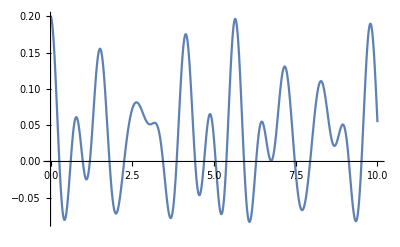

```mathematica
Plot[{Theta1}/.rep,{t,0,10}]
```

It looks like pretty complex behavior! However, this is just a linear combination of the normal modes. Any arbitrary motion of the system can be described as a linear combination of the 6 normal modes.

## Written Problems

-Graphics-